## Bose-Hubbard model simulation

References:
	F. Verstraete, V. Murg, J. I. Cirac
	Matrix product states, projected entangled pair states, and variational renormalization group methods for quantum spin systems
	Advances in Physics 57, 143-224 (2008) DOI

	Thomas Barthel
	Precise evaluation of thermal response functions by optimized density matrix renormalization group schemes
	New Journal of Physics 15, 073010 (2013) DOI

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
SparseIdentityMatrix[d_]:=SparseArray[{i_,i_}->1,{d,d}]
```

```mathematica
SiteCreateOp[M_]:=DiagonalMatrix[Sqrt[Range[1,M]],-1]
SiteAnnihilOp[M_]:=DiagonalMatrix[Sqrt[Range[1,M]],1]
```

```mathematica
NumberOp[M_]:=DiagonalMatrix[Range[0,M]]
```

```mathematica
(* construct Bose-Hamiltonian with open boundary conditions *)
Subscript[H, bose][t_,U_,μ_,M_,1]:=U/2 NumberOp[M].(NumberOp[M]-IdentityMatrix[M+1])-μ NumberOp[M]
Subscript[H, bose][t_,U_,μ_,M_,L_]:=-t Sum[KroneckerProduct[SparseIdentityMatrix[(M+1)^(l-1)],SiteCreateOp[M],SiteAnnihilOp[M],SparseIdentityMatrix[(M+1)^(L-l-1)]]+KroneckerProduct[SparseIdentityMatrix[(M+1)^(l-1)],SiteAnnihilOp[M],SiteCreateOp[M],SparseIdentityMatrix[(M+1)^(L-l-1)]],{l,1,L-1}]+Sum[KroneckerProduct[SparseIdentityMatrix[(M+1)^(l-1)],U/2 NumberOp[M].(NumberOp[M]-IdentityMatrix[M+1])-μ NumberOp[M],SparseIdentityMatrix[(M+1)^(L-l)]],{l,1,L}]
```

### Simulation parameters

```mathematica
(* kinetic hopping parameter *)
Subscript[tH, val]=1;
```

```mathematica
(* interaction strength *)
Subscript[U, val]=5;
```

```mathematica
(* chemical potential *)
Subscript[μ, val]=1/7;
```

```mathematica
(* number of lattice sites *)
Subscript[L, val]=5;
```

```mathematica
(* single site occupation number cut-off *)
Subscript[M, val]=2;
```

```mathematica
(* inverse temperature *)
Subscript[β, val]=3/5;
```

```mathematica
Subscript[t, list]=Range[0,5,1/8];
Length[%]
```

41

### Out-of-time-order correlations

```mathematica
OperatorAverage[A_,H_,β_]:=Module[{expβH=MatrixExp[-β H]},Tr[expβH.A]/Tr[expβH]]
```

```mathematica
GF[A_,B_,H_,β_,t_]:=Module[{expβH=MatrixExp[-β H],At=MatrixExp[-ⅈ t H].A.MatrixExp[ⅈ t H]},Tr[expβH.At.B]/Tr[expβH]]
```

```mathematica
OTOC[A_,B_,C_,D_,H_,β_,t_]:=Module[{expβH=MatrixExp[-β H],At=MatrixExp[-ⅈ t H].A.MatrixExp[ⅈ t H],Ct=MatrixExp[-ⅈ t H].C.MatrixExp[ⅈ t H]},Tr[expβH.At.B.Ct.D]/Tr[expβH]]
```

```mathematica
SiteCreateOpFull[j_,M_,L_]:=KroneckerProduct[SparseIdentityMatrix[(M+1)^j],SiteCreateOp[M],SparseIdentityMatrix[(M+1)^(L-j-1)]]
```

```mathematica
SiteAnnihilOpFull[j_,M_,L_]:=KroneckerProduct[SparseIdentityMatrix[(M+1)^j],SiteAnnihilOp[M],SparseIdentityMatrix[(M+1)^(L-j-1)]]
```

```mathematica
SiteNumberOpFull[j_,M_,L_]:=KroneckerProduct[SparseIdentityMatrix[(M+1)^j],NumberOp[M],SparseIdentityMatrix[(M+1)^(L-j-1)]]
```

```mathematica
Subscript[fn, import]="../output/bose_hubbard/L"<>ToString[Subscript[L, val]]<>"_otoc/bose_hubbard_L"<>ToString[Subscript[L, val]]<>"_M"<>ToString[Subscript[M, val]];
```

```mathematica
(* read simulation results from disk *)
```

```mathematica
Subscript[density, list]=Import[Subscript[fn, import]<>"_density.dat","Real64"]
Dimensions[%]
```

{0.621552,0.675377,0.67607,0.675414,0.621585}

{5}

```mathematica
Subscript[energy, val]=First[Import[Subscript[fn, import]<>"_energy.dat","Real64"]]
```

-1.90681

```mathematica
Subscript[otoc1, list]=First[#]+ⅈ Last[#]&/@Partition[Import[Subscript[fn, import]<>"_otoc1.dat","Real64"],2];
Dimensions[%]
```

{41}

```mathematica
Subscript[otoc2, list]=First[#]+ⅈ Last[#]&/@Partition[Import[Subscript[fn, import]<>"_otoc2.dat","Real64"],2];
Dimensions[%]
```

{41}

```mathematica
Subscript[gf, list]=First[#]+ⅈ Last[#]&/@Partition[Import[Subscript[fn, import]<>"_gf.dat","Real64"],2];
Dimensions[%]
```

{41}

```mathematica
Subscript[i, site]=1;
Subscript[j, site]=3;
```

```mathematica
(* reference calculation *)
```

```mathematica
Block[{tH=Subscript[tH, val],U=Subscript[U, val],μ=Subscript[μ, val],M=Subscript[M, val],L=Subscript[L, val],β=Subscript[β, val],HB},HB=N[Subscript[H, bose][tH,U,μ,M,L]];Subscript[density, list,ref]=Table[OperatorAverage[SiteNumberOpFull[i,M,L],HB,β],{i,0,L-1}]]
```

{0.621553,0.675362,0.676021,0.675362,0.621553}

```mathematica
Block[{tH=Subscript[tH, val],U=Subscript[U, val],μ=Subscript[μ, val],M=Subscript[M, val],L=Subscript[L, val],β=Subscript[β, val],HB},HB=N[Subscript[H, bose][tH,U,μ,M,L]];Subscript[energy, val,ref]=OperatorAverage[HB,HB,β]]
```

-1.9069

```mathematica
Block[{tH=Subscript[tH, val],U=Subscript[U, val],μ=Subscript[μ, val],M=Subscript[M, val],L=Subscript[L, val],β=Subscript[β, val],HB},HB=N[Subscript[H, bose][tH,U,μ,M,L]];Subscript[otoc1, list,ref]=Table[OTOC[SiteCreateOpFull[Subscript[j, site],M,L],SiteCreateOpFull[Subscript[i, site],M,L],SiteAnnihilOpFull[Subscript[j, site],M,L],SiteAnnihilOpFull[Subscript[i, site],M,L],HB,β,t],{t,Subscript[t, list]}]];
```

```mathematica
Block[{tH=Subscript[tH, val],U=Subscript[U, val],μ=Subscript[μ, val],M=Subscript[M, val],L=Subscript[L, val],β=Subscript[β, val],HB},HB=N[Subscript[H, bose][tH,U,μ,M,L]];Subscript[otoc2, list,ref]=Table[OTOC[SiteCreateOpFull[Subscript[j, site],M,L],SiteAnnihilOpFull[Subscript[i, site],M,L],SiteAnnihilOpFull[Subscript[j, site],M,L],SiteCreateOpFull[Subscript[i, site],M,L],HB,β,t],{t,Subscript[t, list]}]];
```

```mathematica
Block[{tH=Subscript[tH, val],U=Subscript[U, val],μ=Subscript[μ, val],M=Subscript[M, val],L=Subscript[L, val],β=Subscript[β, val],HB},HB=N[Subscript[H, bose][tH,U,μ,M,L]];Subscript[gf, list,ref]=Table[GF[SiteCreateOpFull[Subscript[j, site],M,L],SiteAnnihilOpFull[Subscript[i, site],M,L],HB,β,t],{t,Subscript[t, list]}]];
```

```mathematica
(* compare *)
Abs[Subscript[density, list]-Subscript[density, list,ref]]
```

{9.09636×10^-7,0.0000148271,0.0000489787,0.0000516645,0.0000314596}

```mathematica
(* compare *)
Abs[Subscript[energy, val]-Subscript[energy, val,ref]]
```

0.0000860992

```mathematica
(* compare *)
Norm[Subscript[otoc1, list]-Subscript[otoc1, list,ref],∞]
```

0.0000618532

```mathematica
(* compare *)
Norm[Subscript[otoc2, list]-Subscript[otoc2, list,ref],∞]
```

0.0000890692

```mathematica
(* compare *)
Norm[Subscript[gf, list]-Subscript[gf, list,ref],∞]
```

0.0000306323

```mathematica
Subscript[plot, label]="Bose-Hubbard model with\nt_H="<>ToString[Subscript[tH, val]]<>", U="<>ToString[Subscript[U, val]]<>", μ="<>ToString[InputForm[Subscript[μ, val]]]<>", M="<>ToString[Subscript[M, val]]<>", L="<>ToString[Subscript[L, val]]<>", β="<>ToString[N[Subscript[β, val]]]<>"\nsites: i="<>ToString[Subscript[i, site]]<>", j="<>ToString[Subscript[j, site]];
```

```mathematica
Subscript[fn, export]="plots/"<>#<>"/"<>#<>"_"&[FileBaseName[NotebookFileName[]]];
```

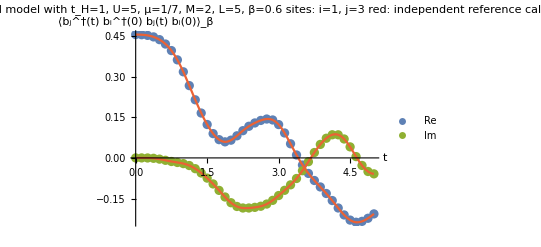

```mathematica
Show[ListPlot[{Transpose[{Subscript[t, list],Re[Subscript[otoc1, list]]}],Transpose[{Subscript[t, list],Im[Subscript[otoc1, list]]}]},AxesLabel->{"t","⟨b_j^†(t) b_i^†(0) b_j(t) b_i(0)⟩_β"},PlotLabel->Subscript[plot, label]<>"\nred: independent reference calculation",PlotStyle->{ColorData[97][1],ColorData[97][3]},PlotLegends->{"Re","Im"}],Plot[{Interpolation[Transpose[{Subscript[t, list],Re[Subscript[otoc1, list,ref]]}]][τ],Interpolation[Transpose[{Subscript[t, list],Im[Subscript[otoc1, list,ref]]}]][τ]},{τ,0,5},PlotRange->All,PlotStyle->ColorData[97][4]]]
Export[Subscript[fn, export]<>"otoc1_L"<>ToString[Subscript[L, val]]<>".pdf",%];
```

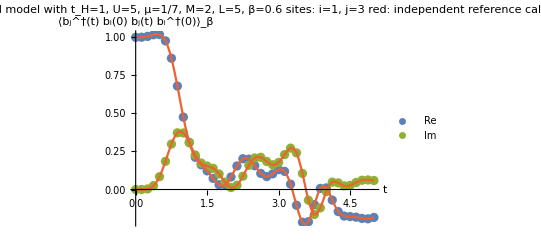

```mathematica
Show[ListPlot[{Transpose[{Subscript[t, list],Re[Subscript[otoc2, list]]}],Transpose[{Subscript[t, list],Im[Subscript[otoc2, list]]}]},AxesLabel->{"t","⟨b_j^†(t) b_i(0) b_j(t) b_i^†(0)⟩_β"},PlotLabel->Subscript[plot, label]<>"\nred: independent reference calculation",PlotStyle->{ColorData[97][1],ColorData[97][3]},PlotLegends->{"Re","Im"}],Plot[{Interpolation[Transpose[{Subscript[t, list],Re[Subscript[otoc2, list,ref]]}]][τ],Interpolation[Transpose[{Subscript[t, list],Im[Subscript[otoc2, list,ref]]}]][τ]},{τ,0,5},PlotRange->All,PlotStyle->ColorData[97][4]]]
Export[Subscript[fn, export]<>"otoc2_L"<>ToString[Subscript[L, val]]<>".pdf",%];
```

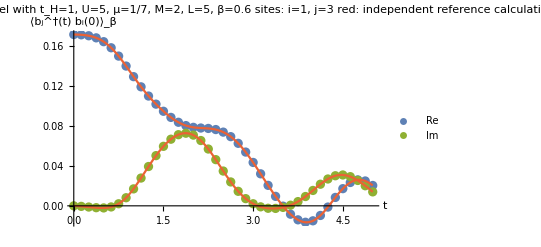

```mathematica
Show[ListPlot[{Transpose[{Subscript[t, list],Re[Subscript[gf, list]]}],Transpose[{Subscript[t, list],Im[Subscript[gf, list]]}]},AxesLabel->{"t","⟨b_j^†(t) b_i(0)⟩_β"},PlotLabel->Subscript[plot, label]<>"\nred: independent reference calculation",PlotStyle->{ColorData[97][1],ColorData[97][3]},PlotLegends->{"Re","Im"}],Plot[{Interpolation[Transpose[{Subscript[t, list],Re[Subscript[gf, list,ref]]}]][τ],Interpolation[Transpose[{Subscript[t, list],Im[Subscript[gf, list,ref]]}]][τ]},{τ,0,5},PlotRange->All,PlotStyle->ColorData[97][4]]]
Export[Subscript[fn, export]<>"gf_L"<>ToString[Subscript[L, val]]<>".pdf",%];
```

### Virtual bond dimensions

```mathematica
Subscript[t, plot]={0,1/2,1,2,4,5};
```

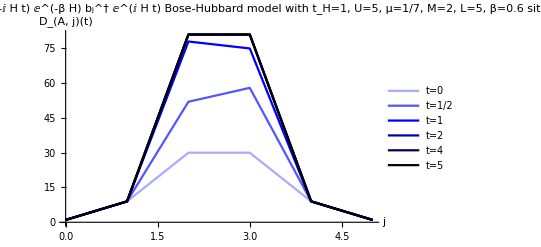

```mathematica
(* virtual bond dimension for 'A' operator *)
Partition[Import[Subscript[fn, import]<>"_DXA.dat","Integer64"],Subscript[L, val]+1];
%⟦#⟧&/@Flatten[Position[Subscript[t, list],#]&/@Subscript[t, plot]];
ListLinePlot[Transpose[{Range[0,Subscript[L, val]],#}]&/@%,AxesLabel->{"j","D_(A, j)(t)"},PlotRange->All,PlotLabel->"virtual bond dimension of ⅇ^(-ⅈ H t) ⅇ^(-β H) b_j^† ⅇ^(ⅈ H t)\n"<>Subscript[plot, label],PlotStyle->{Lighter[Blue,2/3],Lighter[Blue,1/3],Blue,Darker[Blue,1/3],Darker[Blue,2/3],Black},PlotLegends->("t="<>ToString[InputForm[#]]&/@Subscript[t, plot])]
Export[Subscript[fn, export]<>"DA_L"<>ToString[Subscript[L, val]]<>"_M"<>ToString[Subscript[M, val]]<>".pdf",%];
```

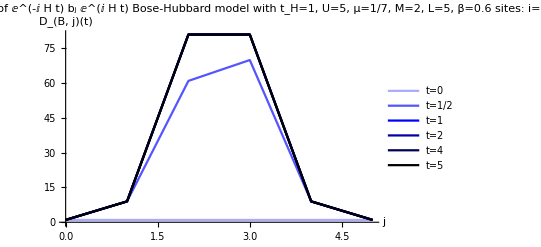

```mathematica
(* virtual bond dimension for 'B' operator *)
Partition[Import[Subscript[fn, import]<>"_DXB.dat","Integer64"],Subscript[L, val]+1];
%⟦#⟧&/@Flatten[Position[Subscript[t, list],#]&/@Subscript[t, plot]];
ListLinePlot[Transpose[{Range[0,Subscript[L, val]],#}]&/@%,AxesLabel->{"j","D_(B, j)(t)"},PlotRange->All,PlotLabel->"virtual bond dimension of ⅇ^(-ⅈ H t) b_j ⅇ^(ⅈ H t)\n"<>Subscript[plot, label],PlotStyle->{Lighter[Blue,2/3],Lighter[Blue,1/3],Blue,Darker[Blue,1/3],Darker[Blue,2/3],Black},PlotLegends->("t="<>ToString[InputForm[#]]&/@Subscript[t, plot])]
Export[Subscript[fn, export]<>"DB_L"<>ToString[Subscript[L, val]]<>"_M"<>ToString[Subscript[M, val]]<>".pdf",%];
```

### Effective truncation weight

```mathematica
(* tolerance (truncation weight) for ⅇ^(-β H) *)
Norm[Partition[Import[Subscript[fn, import]<>"_tol_eff_beta.dat","Real64"],Subscript[L, val]-1]-10^-10]
```

0.

```mathematica
(* tolerance (truncation weight) for ⅇ^(-ⅈ H t) ⅇ^(-β H) Subscript[b, j]^† ⅇ^(ⅈ H t) *)
Norm[Partition[Import[Subscript[fn, import]<>"_tol_eff_A.dat","Real64"],Subscript[L, val]-1]-10^-10]
```

0.

```mathematica
(* tolerance (truncation weight) for ⅇ^(-ⅈ H t) Subscript[b, j] ⅇ^(ⅈ H t) *)
Norm[Partition[Import[Subscript[fn, import]<>"_tol_eff_B.dat","Real64"],Subscript[L, val]-1]-10^-10]
```

0.